```mathematica
Needs["FeynArts`"]
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
tops=CreateTopologies[0,2->2];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram



FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
Paint@tops
```

```mathematica
ins=InsertFields[tops,{V[1],V[5]}->{F[3],-F[3]},Model->"SMQCD"]
```

loading generic model file /home/Felix/Physik/Mathematica/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/Felix/Physik/Mathematica/FeynArts/Models/SMQCD.mod

loading classes model file /home/Felix/Physik/Mathematica/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 1 Generic, 1 Classes insertions

> Top. 4: 1 Generic, 1 Classes insertions

in total: 2 Generic, 2 Classes insertions

TopologyList[Process→{V[1],V[5,{Glu2}]}→{F[3,{Gen3,Col3}],-F[3,{Gen4,Col4}]},Model→{SMQCD},GenericModel→{Lorentz},InsertionLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→V[5,{Glu2}],Field[3]→-F[3,{Gen3,Col3}],Field[4]→F[3,{Gen4,Col4}],Field[5]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→V[5,{Glu2}],Field[3]→-F[3,{Gen3,Col3}],Field[4]→F[3,{Gen4,Col4}],Field[5]→-F[3,{Gen3,Col3}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→V[1],Field[2]→V[5,{Glu2}],Field[3]→-F[3,{Gen3,Col3}],Field[4]→F[3,{Gen4,Col4}],Field[5]→F]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→V[1],Field[2]→V[5,{Glu2}],Field[3]→-F[3,{Gen3,Col3}],Field[4]→F[3,{Gen4,Col4}],Field[5]→F[3,{Gen3,Col4}]]]]]

> Top. 1: 1 diagram

> Top. 2: 1 diagram

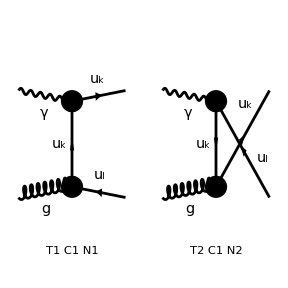

FeynArtsGraphics[{\gamma,g}→{ComposedChar[u,k],ComposedChar[u,l]}][([T1 C1 N1] | [T2 C1 N2]
Null | Null)]

```mathematica
Paint[ins,ColumnsXRows->2,PaintLevel->{Classes}]
```

```mathematica
Needs["FormCalc`"]
```

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

/home/Felix/Physik/Mathematica/FormCalc/Linux-x86-64/ReadForm

$Aborted

```mathematica
born=CalcFeynAmp[CreateFeynAmp[ins]]
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

in total: 2 Generic, 2 Classes amplitudes

CalcFeynAmp[FeynAmpList[Process→{{V[1],p1,0,{}},{V[5,{Glu2}],p2,0,{√3 ColorCharge}}}→{{F[3,{Gen3,Col3}],k1,MQU[Gen3],{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{Gen4,Col4}],k2,MQU[Gen4],{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}},Model→{SMQCD},GenericModel→{Lorentz},AmplitudeLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1],Integral[],-RelativeCF ū[k1,MQU[Gen3]].(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).(gs[p2-k2]+Mass[F[Gen5],Internal]).(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).v[k2,MQU[Gen4]] ep[V[1],p1,Lor1] ep[V[5,{Glu2}],p2,Lor2] 1/((-(p2)+k2)^2-Mass[F[Gen5],Internal]^2),{Mass[F[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{MQU[Gen3],-ⅈ GS SUNT[Glu2,Col3,Col4],-ⅈ GS SUNT[Glu2,Col3,Col4],-(2 ⅈ EL)/3,-(2 ⅈ EL)/3,IndexDelta[Gen3,Gen4] SumOver[Col3,3,External] SumOver[Col4,3,External] SumOver[Gen3,3,External] SumOver[Gen4,3,External] SumOver[Glu2,8,External]}]],FeynAmp[GraphID[Topology==2,Generic==1],Integral[],-RelativeCF ū[k1,MQU[Gen3]].(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).(gs[-(p2)+k1]+Mass[F[Gen5],Internal]).(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).v[k2,MQU[Gen4]] ep[V[1],p1,Lor1] ep[V[5,{Glu2}],p2,Lor2] 1/((p2-k1)^2-Mass[F[Gen5],Internal]^2),{Mass[F[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{MQU[Gen3],-(2 ⅈ EL)/3,-(2 ⅈ EL)/3,-ⅈ GS SUNT[Glu2,Col3,Col4],-ⅈ GS SUNT[Glu2,Col3,Col4],IndexDelta[Gen3,Gen4] SumOver[Col3,3,External] SumOver[Col4,3,External] SumOver[Gen3,3,External] SumOver[Gen4,3,External] SumOver[Glu2,8,External]}]]]]